```mathematica
(*mub=1307.5/(1+0.288*s)
```

```mathematica
(*tc=158.4/(1+Exp[2.60-Log[s]/0.45])
```

```mathematica
(*f={mub==a/(1+b*s),tc==e/(1+Exp[c-Log[s]/d])}
```

```mathematica
(*f2=Eliminate[f,s]//FullSimplify
```

```mathematica
(*Solve[f2,tc,Reals]//Simplify
```

```mathematica
tc=e/(1+Exp[c-Log[a/(b d mub)-1/(b d)]])
```

e/(1+ⅇ^c/(-1/(b d)+a/(b d mub)))

```mathematica
Tc={167.8,164.3,159.9,159.8,157.5,150.6,143.8};
muB={27.0,69.2,104.7,151.9,195.6,292.5,399.8};
Tc={159.9,159.8,157.5,150.6};
muB={104.7,151.9,195.6,292.5};data=Transpose[{muB,Tc}]
```

{{104.7,159.9},{151.9,159.8},{195.6,157.5},{292.5,150.6}}

```mathematica
fitline=NonlinearModelFit[data,{e/(1+Exp[c-Log[a/(b d x)-1/(b d)]]),a>0},{a,b,c,d,e},x]
```

FittedModel[-887.669/(1+(«56»)/(-5.09001×10^-7+(«23»)/x))]

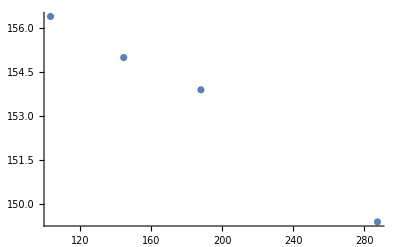

```mathematica
ListPlot[data]
```

```mathematica
Normal[fitline]
```

1.00734/(1+(5.37817365153×10^608)/(-5.09001×10^-7+(5.08954×10^-6)/x))

```mathematica
tc2[mub2_]:=1.0073380292036989/(1+(5.378173651528706767727039693192`12.807948922996626*^608)/(-5.090006132863423*^-7+(5.089539102763219*^-6)/mub2))
```

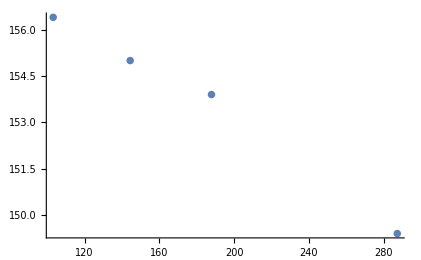

```mathematica
Show[ListPlot[data],Plot[tc2[x],{x,0,400}]]
```

```mathematica
tf={164.3,160.3,156.4,155.0,153.9,149.4,144.3};
s={200.,62.4,39.0,27.0,19.6,11.5,7.7};
datats=Transpose[{s,tf}]
```

{{200.,164.3},{62.4,160.3},{39.,156.4},{27.,155.},{19.6,153.9},{11.5,149.4},{7.7,144.3}}

```mathematica
158.4/(1+13.463738035001692/(-3.4722222222222223+4539.930555555556/x)^2.2222222222222223)
```

```mathematica
fitts=NonlinearModelFit[data,{a/(1+b/(c+d/x)^e),150.<a<170.,1.<b<30.,-10.<c<0,2000<d<6000,0<e<10},{a,b,c,d,e},x]
```

FittedModel[160.519/(1+29.9996/(-«19»+«1»)^(«19»))]

```mathematica
fitts=NonlinearModelFit[data,a/(1+b/(c+d/x)^e),{a,b,c,d,e},x]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[1.7459/(1-5.38949/(«19»-«1»)^(«19»))]

```mathematica
Normal[fitts]
```

160.519/(1+29.9996/(-0.183253+2000.01/x)^3.22863)

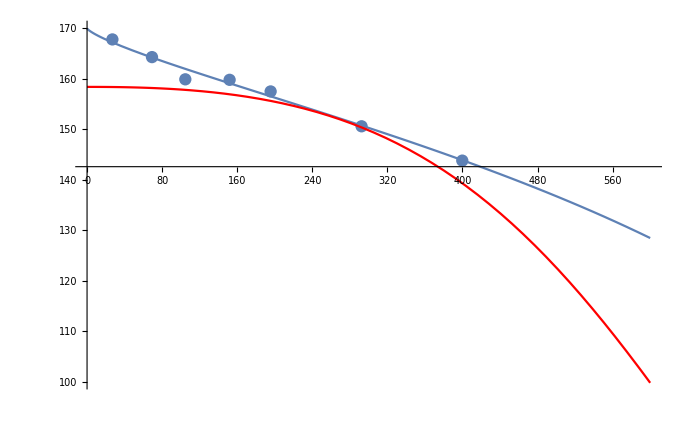

```mathematica
Show[ListPlot[data],Plot[160.51884386546163/(1+29.999587626838213/(-0.1832526600002549+2000.0085014152924/s1)^3.2286289635092587),{s1,0,600}],Plot[158.4/(1+13.463738035001692/(-3.4722222222222223+4539.930555555556/s1)^2.2222222222222223),{s1,0,600},PlotStyle->Red],PlotRange->{{0,600},{100,170}}]
```

```mathematica
158.4/(1+Exp[2.6-Log[s2/0.45]])
```

158.4/(1+6.05868/s2)

```mathematica
158.4/(1+Exp[2.6-Log[1307.5/(x*0.288)-1/0.288]/0.45])
```

158.4/(1+13.4637/(-3.47222+4539.93/x)^2.22222)

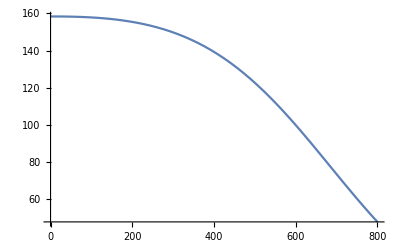

```mathematica
Plot[158.4/(1+Exp[2.6-Log[1307.5/(x*0.288)-1/0.288]/0.45]),{x,0,800}]
```